# Iteration 1: Basic SZR Model

## Non-Dimensionalised

The non-dimensionalised system of equations is given by:
	H’[t] == - H[t] Z[t]
    	Z’[t] == H[t] Z[t] - δZ Z[t]
   	 R’[t] == δZ Z[t]
   	 
Where δZ is the dimensionless zombie removal rate.

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, R, t, Hfunc, Zfunc, Rfunc, fixedPoints, 
   phasePlotHZ, phasePlotZR, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == - H[t] Z[t],
    Z'[t] == H[t] Z[t] - δZ Z[t],
    R'[t] == δZ Z[t]
  };
  
  jMatrix = {
   {-Z, - H, 0},
   {0, (H - δZ), 0},
   {0, δZ, 0}
	};
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0/H0, 
     Z[0] == Z0/H0, 
     R[0] == R0/H0
    }, 
    {H, Z, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
(*  Print[traceJ];*)
  detJ = Det[jMatrix];
(*  Print[detJ];*)
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  
  (* Generate phase space stream plots *)
  phasePlotHZ = 
   StreamPlot[
    Evaluate[{
      - H Z, 
      H Z - δZ Z
    }],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
   phasePlotZR = 
   StreamPlot[
    Evaluate[{
      H Z - δZ Z,
      δZ Z
    } /. {H -> Hfunc[tmax]}],
    {Z, 0, 1}, {R, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Z (Zombies)", "R (Removed)"},
    Frame -> True,
    FrameLabel -> {"Z (Zombies)", "R (Removed)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (H)", "Zombies (Z)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotZR,
    Show[
		parameterSpace,
		ListPlot[{{finalDetJ,finalTraceJ}},PlotStyle->PointSize[Large]],
		Frame -> True,
		FrameLabel -> {"Determinant", "Trace"}
	]
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{δZ, 1.1, "Dimensionless zombie removal rate (delta_Z)"}, 0, 2, 0.01},
 {{H0, 500, "Initial humans (H0)"}, 0, 5000, 1},
 {{Z0, 100, "Initial zombies (Z0)"}, 0, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 100, "Simulation time"}, 10, 1000000, 1}
]
```

## Eigen Analysis

```mathematica
jMatrix = {
   {-Z, - H, 0},
   {Z, (H - δZ), 0},
   {0, δZ, 0}
	};

fixedPoint1 = {Z -> 0};
fixedPoint2 = {H -> 0, Z -> 0};

genEigenVals = Eigenvalues[jMatrix];
genEigenVects = Eigenvectors[jMatrix];
eigenValsP1 = Eigenvalues[jMatrix /. fixedPoint1]
eigenValsP2 = Eigenvalues[jMatrix /. fixedPoint2]
```

{0,0,H-δZ}

{-δZ,0,0}

## Bifurcation

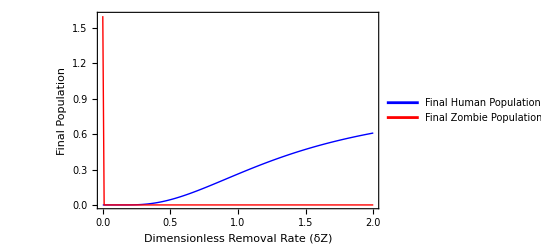

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, finalH, finalZ},
    (* Define the differential equations *)
    eqns = {
      H'[t] == - H[t] Z[t],
      Z'[t] == H[t] Z[t] - δZ Z[t],
      R'[t] == δZ Z[t]
    };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns, 
       H[0] == 500/500, 
       Z[0] == 300/500,
       R[0] == 0/500
      },
      {H, Z, R}, 
      {t, 0, 10000}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[10000];
    finalZ = Zfunc[10000];
    
    (* Return the deltaZ and final values for plotting *)
    {δZ, finalH, finalZ}
  ],
  {δZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}]
  },
  PlotRange -> All,
  PlotLegends -> {"Final Human Population (H)", "Final Zombie Population (Z)"},
  PlotStyle -> {{Blue, Thick}, {Red, Thick}},
  AxesLabel -> {"Zombie Removal Rate (δZ)", "Final Population"},
  Frame -> True,
  FrameLabel -> {"Dimensionless Removal Rate (δZ)", "Final Population"}
]
```